```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY207/sec_int_data/412nm.dat"]
```

{{1.65577,-0.311879},{1.59352,-0.292172},{1.51672,-0.247936},{1.46373,-0.18223},{1.42047,-0.162201},{1.37769,-0.124611},{1.34607,-0.102553},{1.31418,-0.0943107},{1.27734,-0.0923456},{1.24989,-0.11034},{1.21939,-0.0714101},{1.20221,-0.0804511},{1.18519,-0.137195},{1.17023,-0.153396},{1.1572,-0.184091},{1.14604,-0.220771},{1.13497,-0.253152},{1.12762,-0.423074},{1.12192,-0.400776},{1.11852,-0.333084},{1.11638,-0.300686},{1.11532,-0.311865},{1.11466,-0.11485},{1.11691,-0.0741418},{1.12052,0.0107421},{1.12514,0.0479327},{1.15252,-0.0118904},{1.18204,-0.0429284},{1.20774,0.0141001},{1.24068,0.0280042},{1.28541,-0.00639038},{1.36328,-0.0407595},{1.4246,-0.0852203}}

-0.0597861-0.06994 x

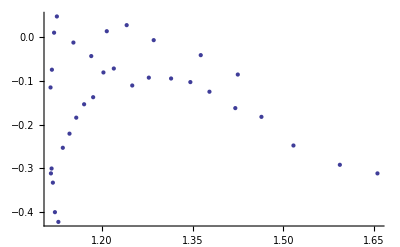

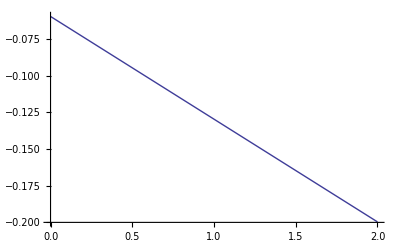

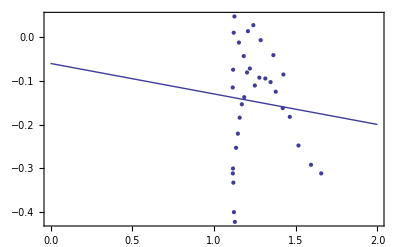

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```